```mathematica
test630=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\1000umclistaltalt.txt","Table"];
```

```mathematica
test6300=test630[[All,{1,2,3,6,7,9,10,11,12,13}]];
```

```mathematica
test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]=Round[test6300[[2;;Length[test6300],{1,2,3,4,5,6}]]];
```

```mathematica
test6300[[2;;Length[test6300],{8}]]=N[test6300[[2;;Length[test6300],{8}]]-750];
```

```mathematica
test6300[[2;;Length[test6300],{10}]]=N[test6300[[2;;Length[test6300],{10}]]-963];
```

```mathematica
test6300[[2;;Length[test6300],{3}]]=N[test6300[[2;;Length[test6300],{3}]]*1/60];
```

```mathematica
test6300cut=removefljumps[test6300];
```

RFP Mean = -0.65333
RFP high = 194.137
RFP max = 1437.65
RFP low = -195.444
RFP min = -1404.55
YFP mean = -0.0847033
YFP high = 124.542
YFP max = 139.406
YFP low = -124.711
YFP min = -152.263

```mathematica
linstest6300cut=lineagefinder[test6300cut];//AbsoluteTiming
```

{18.4527,Null}

```mathematica
comblintest630=combinelineages2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{36.4748,Null}

```mathematica
comblinmultiplytest630=combinelineagesmulitply2fl[test6300,linstest6300cut];//AbsoluteTiming
```

{34.19,Null}

```mathematica
growthtest630noextrap=growthratecalcsupnoextrap[comblinmultiplytest630,30,comblintest630];//AbsoluteTiming
```

387

{5.76435,Null}

```mathematica
testset=RandomChoice[Table[i,{i,1,320}],50]
```

{252,65,293,172,148,114,31,74,216,287,225,34,120,164,156,160,261,29,150,202,160,203,148,277,137,14,40,191,174,224,43,210,46,214,104,93,187,268,149,286,171,184,4,93,120,112,23,223,208,119}

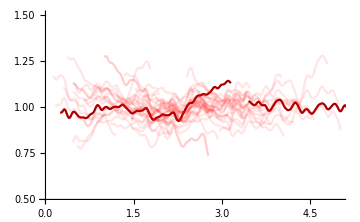

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,{313,123}],PlotRange->{{0,5},{0.5,1.5}},PlotStyle->Darker[Red],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,1]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],Red]]}]
```

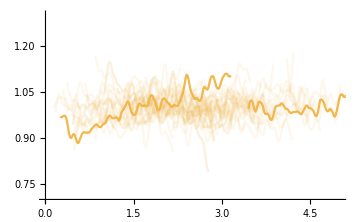

```mathematica
Show[{ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,{313,123}],PlotRange->{{0,5},{0.7,1.3}},PlotStyle->RGBColor["#f2b74d"],ImageSize->Medium,AxesStyle->Directive[Black,20]],ListLinePlot[Map[plotalllin2[#,growthtest630noextrap,3]&,testset],PlotRange->All,PlotStyle->Directive[Opacity[0.1],RGBColor["#f2b74d"]]]}]
```

```mathematica
{iptg1mmgrowthACF30minwindowsmooth,iptg1mmmcACF30minwindowsmooth,iptg1mmbetaxACF30minwindowsmooth,iptg1mmmcgrowthCCCF30minwindowsmooth,iptg1mmbetaxgrowthCCCF30minwindowsmooth,iptg1mmmcbetaxCCCF30minwindowsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1mmiptgacfcccf30minwindowsmoothfull.txt","Table"];
```

```mathematica
metabsim=metabgensteadystate[0,2.1,0,0,0,14,0.02,2000,0.2,1];//AbsoluteTiming
```

{472.106,Null}

```mathematica
keepMetabSS=keepallmetabmaintainsteadystate[metabsim[[1]],0,2.1,0,0,0,0,0,0,0,0,14,0.02];//AbsoluteTiming
```

{1181.14,Null}

```mathematica
metabsimMemory=metabproteinmemfast[keepMetabSS];
```

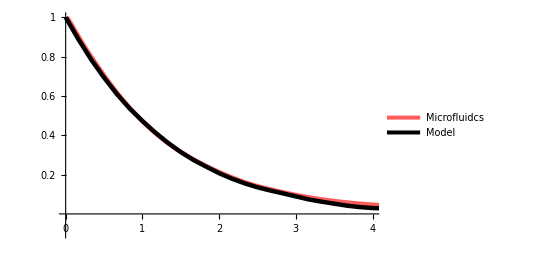

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1mmmcACF30minwindowsmooth]}],iptg1mmmcACF30minwindowsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[1]]]},PlotRange->{{0,4},{-.1,1}},PlotLegends->Placed[{"Microfluidcs","Model"},Right],PlotStyle->{{Thickness[0.008],RGBColor[1,0.36,0.36]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
{iptg1000um630growthACFsmooth,iptg1000um630mcACFsmooth,iptg1000um630betaxACFsmooth}=Import["C:\\Users\\Zhang Lab\\Desktop\\New folder\\1000um630ACFsmooth.txt","Table"];
```

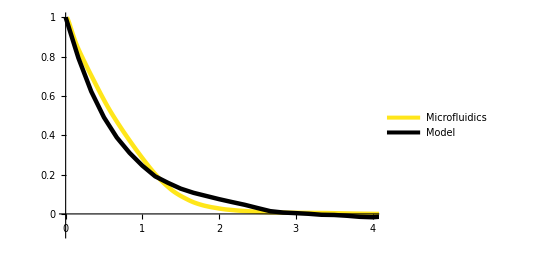

```mathematica
ListLinePlot[{Transpose@{Table[i/60,{i,1,Length[iptg1000um630betaxACFsmooth]}],iptg1000um630betaxACFsmooth},Map[{#[[1]],#[[2]]}&,metabsimMemory[[3]]]},PlotRange->{{0,4},{-.1,1}},
PlotLegends->Placed[{"Microfluidics","Model"},Right],
PlotStyle->{{Thickness[0.008],RGBColor[1,0.9,0.1]},{Thickness[0.008],Black}},AxesStyle->Directive[Black, 20],Ticks->{Automatic,{0,0.2,0.4,0.6,0.8,1}},AspectRatio->.65]
```

```mathematica
exp227rawdata=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\iptg1mmrawtxt.txt","Table"];//AbsoluteTiming
```

{3.65076,Null}

```mathematica
testexp227cut=removefljumps[exp227rawdata];
```

RFP Mean = -0.438949
RFP high = 812.338
RFP max = 18401.5
RFP low = -813.215
RFP min = -23766.4
YFP mean = -0.0150807
YFP high = 153.572
YFP max = 1288.14
YFP low = -153.602
YFP min = -1250.99

```mathematica
linstestexp227cut=lineagefinder[testexp227cut];//AbsoluteTiming
```

{46.3093,Null}

```mathematica
combliniptg1mm=combinelineages2fl[exp227rawdata,linstestexp227cut];//AbsoluteTiming
```

{131.42,Null}

```mathematica
lowprodmc=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],6]],combliniptg1mm[[181]][[All,6]]];
```

```mathematica
lowprodbx=Join[combliniptg1mm[[180]][[77;;Length[combliniptg1mm[[180]]],7]],combliniptg1mm[[181]][[All,7]]];
```

```mathematica
midprodmc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],6]],combliniptg1mm[[85]][[All,6]]];
```

```mathematica
midprodbc=Join[combliniptg1mm[[84]][[29;;Length[combliniptg1mm[[84]]],7]],combliniptg1mm[[85]][[All,7]]];
```

```mathematica
highprodmc=combliniptg1mm[[100]][[All,6]];
```

```mathematica
highprodbx=combliniptg1mm[[100]][[All,7]];
```

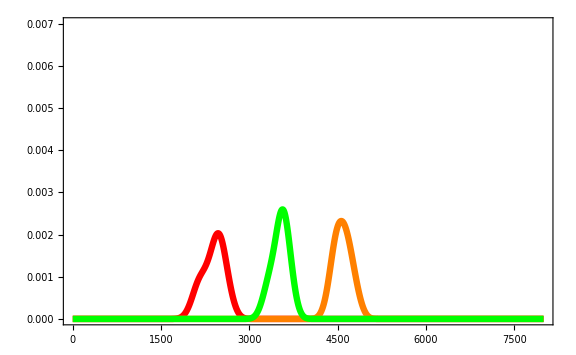
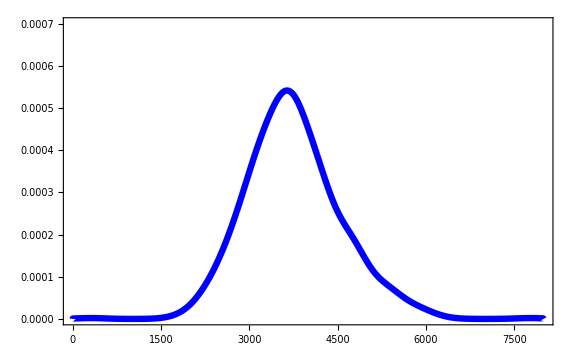
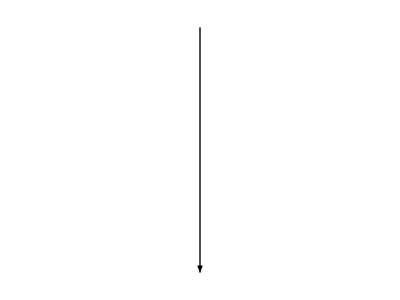

```mathematica
Overlay[{SmoothHistogram[{lowprodmc,midprodmc,highprodmc},100,PlotRange->{{0,8000},{0,0.007}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,6]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],250,PlotRange->{{0,8000},{0,0.0007}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

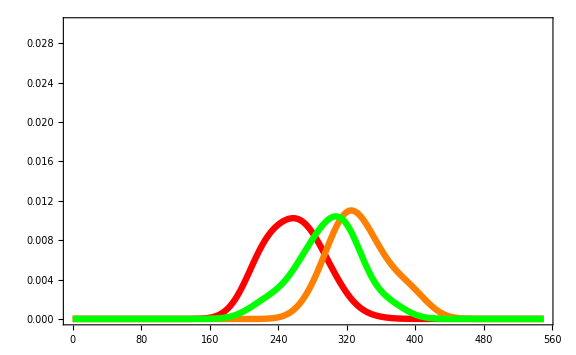
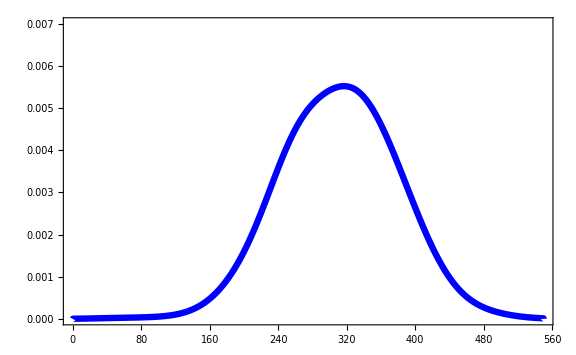

```mathematica
Overlay[{SmoothHistogram[Map[combliniptg1mm[[#]][[All,7]]&,{180,84,100}],20,PlotRange->{{0,550},{0,0.03}},PlotStyle->{{Thickness[0.008],Red},{Thickness[0.008],Orange},{Thickness[0.008],Green}},ImageSize->Large,Frame->{True,False,False,False},FrameStyle->Directive[Black,25]],SmoothHistogram[Map[combliniptg1mm[[#]][[1,7]](*/3770*)&,Table[i,{i,Length[combliniptg1mm]}]],30,PlotRange->{{0,550},{0,0.007}},PlotStyle->{Thickness[0.008],Blue},ImageSize->Large,Frame->{True,False,False,False,False},FrameStyle->Directive[Black,25]]}]
```

```mathematica
transition=highlowtransitionovertime[combliniptg1mm];
```

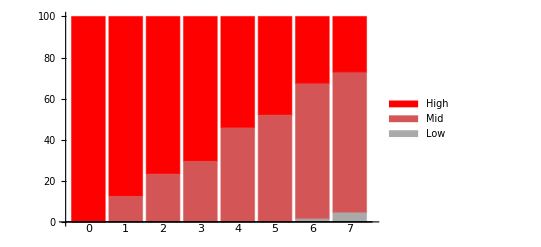

```mathematica
BarChart[transition[[2]],ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}]
```

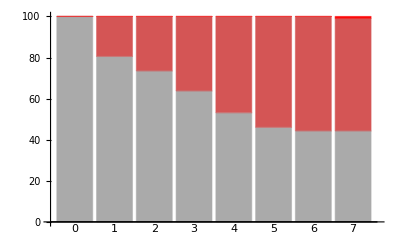

```mathematica
BarChart[transition[[1]],ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Red},.5],Red},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20}]
```

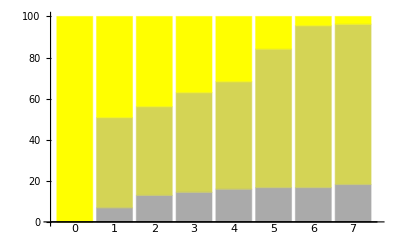

```mathematica
BarChart[transition[[4]],ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20}]
```

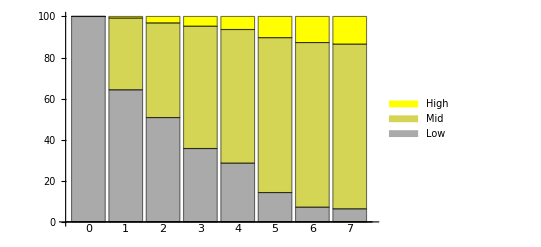

```mathematica
BarChart[transition[[3]],ChartLayout->"Percentile",ChartStyle->{Lighter[Gray],Blend[{Lighter[Gray],Yellow},.5],Yellow},ChartLabels->{{"0","1","2","3","4","5","6","7"},None},LabelStyle->{Black,20},ChartLegends->{"Low","Mid","High"}]
```